In this notebook, we compute the eigenvalues for a two-delay DDE.  This requires an asymptotic expansion and the expansion needs to satisfy certain inequalities to be accurate.  These inequalities are defined in terms of combinations of the original parameters.  The  functions with a ‘2’ at the end are

```mathematica
Clear[Logn,f2p,f2p2,z,j,w,tau1,tau2,tau2p,lamk,lamk2,lamk3,sk,sk2,z,j,w,alpha,beta,gamma,alpha1,beta2,gamma2,tau,tau1,tau2,k,l,m,n,p,q,mmax,kmax,kk,kkmax]
Logn[z_,j_] := Log[Abs[z]]+Arg[z]+2Pi I j;
f2p[w_,tau1_,tau2_,j_,c_] := (-1)^j (E^-w +c E^(-w tau1/tau2)/((tau2/tau1)^j));
f2p2[w_,tau_,j_,c_] := (-1)^j (E^-w +c E^(-w/tau)/((tau)^j));
```

```mathematica
Clear[DBellYq,DBellYq2]
DBellYq[l_,p_,q_,tau1_,tau2_,c_] := DBellYq[l,p,q,tau1,tau2,c]=
If[l<0||p<0||(p==0&&l>0)||l<p,0,
If[q==0,BellY[l,p,Array[f2p[0,tau1,tau2,#1,c]&,{l-p+1}]],
Sum[Binomial[l,r] Sum[Binomial[q-1,s]DBellYq[l-r,p-1,q-1-s,tau1,tau2,c] f2p[0,tau1,tau2,1+r+s,c],{s,0,q-1}],{r,1,l-p+1}]]];
DBellYq2[l_,p_,q_,tau_,c_] := DBellYq2[l,p,q,tau,c]=
If[l<0||p<0||(p==0&&l>0)||l<p,0,
If[q==0,BellY[l,p,Array[f2p2[0,tau,#1,c]&,{l-p+1}]],
Sum[Binomial[l,r] Sum[Binomial[q-1,s]DBellYq2[l-r,p-1,q-1-s,tau,c] f2p2[0,tau,1+r+s,c],{s,0,q-1}],{r,1,l-p+1}]]];
```

```mathematica
Clear[numerfcn,numerfcn2]
numerfcn[l_,m_,p_,tau1_,tau2_,c_]:=numerfcn[l,m,p,tau1,tau2,c]=Sum[Binomial[2 m-2-l,q](m-1-p)! BellY[2 m-2-l-q,m-1-p,Array[f2p[0,tau1,tau2,#1,c]&,{Max[0,m-l-q+p]}]]DBellYq[l,p,q,tau1,tau2,c],{q,0,2 m-2-l}];
numerfcn2[l_,m_,p_,tau_,c_]:=numerfcn2[l,m,p,tau,c]=Sum[Binomial[2 m-2-l,q](m-1-p)! BellY[2 m-2-l-q,m-1-p,Array[f2p2[0,tau,#1,c]&,{Max[0,m-l-q+p]}]]DBellYq2[l,p,q,tau,c],{q,0,2 m-2-l}];
```

```mathematica
Clear[aklm,atildeklm,bkmp]
aklm[k_,l_,m_] := Binomial[m-1,l] (m+k)!/(k+l+1)!;
atildeklm[k_,l_,m_] := aklm[k,l,m] Binomial[2 m+k-1,2 m-l-2] (k+1+l)!;
bkmp[k_,m_,p_] := (-1)^(p) Pochhammer[m+k,p];
```

```mathematica
Clear[Numer,Numer2]
Numer[m_,k_,tau1_,tau2_,c_]:=Numer[m,k,tau1,tau2,c]=Sum[atildeklm[k,l,m] Sum[bkmp[k,m,p]numerfcn[l,m,p,tau1,tau2,c],{p,0,l}],{l,0,m-1}];
Numer2[m_,k_,tau_,c_]:=Numer2[m,k,tau,c]=Sum[atildeklm[k,l,m] Sum[bkmp[k,m,p]numerfcn2[l,m,p,tau,c],{p,0,l}],{l,0,m-1}];
```

```mathematica
Clear[Denom,Denom2]
Denom[m_,k_,tau1_,tau2_,c_] :=(2 m+k-1)! f2p[0,tau1,tau2,1,c]^(2 m+k-1);
Denom2[m_,k_,tau_,c_] :=(2 m+k-1)! f2p2[0,tau,1,c]^(2 m+k-1);
```

```mathematica
Clear[h,h2]
h[m_,k_,tau1_,tau2_,c_] := h[m,k,tau1,tau2,c]=Numer[m,k,tau1,tau2,c]/Denom[m,k,tau1,tau2,c];h2[m_,k_,tau_,c_] := h2[m,k,tau,c]=Numer2[m,k,tau,c]/Denom2[m,k,tau,c];
```

```mathematica
Clear[sigma,sigma2]
sigma[alpha_,gamma_,tau1_,tau2_,j_]  :=1/Logn[gamma tau1 Exp[-alpha tau2],j];
sigma2[gamma2_,j_] :=1/Logn[gamma2,j];
```

```mathematica
Clear[c,c2]
c[alpha_,beta_,gamma_,tau1_,tau2_,j_] := (beta Exp[alpha (tau2-tau1)]/gamma)(gamma tau2 Exp[-alpha tau2]/Logn[gamma tau1 Exp[-alpha tau2],j])^(1-tau1/tau2);
c2[beta2_,gamma2_,tau_,j_] := (beta2/gamma2)(gamma2 tau /(Logn[gamma2,j]))^((tau-1)/tau);
```

```mathematica
Clear[mu,mu2]
mu[alpha_,beta_,gamma_,tau1_,tau2_,j_] := (Log[tau2/tau1]+Log[1/Logn[gamma tau1 Exp[-alpha tau2],j]])/Logn[gamma tau1 Exp[-alpha tau2],j]-c[alpha,beta,gamma,tau1,tau2,j];
mu2[beta2_,gamma2_,tau_,j_] := (Log[tau]+Log[1/Logn[gamma2,j]])/Logn[gamma2,j]-c2[beta2,gamma2,tau,j];
```

```mathematica
Clear[vfun,vfuncomp,vfun2,vfun2comp]
vfun[mu_,sigma_,mmax_,kmax_,tau1_,tau2_,c_]:=vfun[mu,sigma,mmax,kmax,tau1,tau2,c]=Sum[Sum[ Pochhammer[m,k] h[m,k,tau1,tau2,c] mu^m sigma^k/m!/k!,{m,1,mmax}],{k,0,kmax}];vfuncomp = Compile[{{mu,_Complex},{sigma,_Complex},{mmax,_Integer},{kmax,_Integer},{tau1,_Real},{tau2,_Real},{c,_Complex}},vfun[mu,sigma,mmax,kmax,tau1,tau2,c],RuntimeAttributes->{Listable},Parallelization->True];
vfun2[beta2_,gamma2_,mmax_,kmax_,tau_,j_]:=vfun2[beta2,gamma2,mmax,kmax,tau,j]=Sum[Sum[Pochhammer[m,k] h2[m,k,tau,c2[beta2,gamma2,tau,j]] mu2[beta2,gamma2,tau,j]^m sigma2[gamma2,j]^k/m!/k!,{m,1,mmax}],{k,0,kmax}];
vfun2comp = Compile[{{beta2,_Complex},{gamma2,_Complex},{mmax,_Integer},{kmax,_Integer},{tau,_Real},{j,_Integer}},vfun2[beta2,gamma2,mmax,kmax,tau,j],{{_,_Complex}},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
Clear[sk,sk2,skComp,sk2Comp]
sk[alpha_,beta_,gamma_,tau1_,tau2_,j_,mmax_,kkmax_] := sk[alpha,beta,gamma,tau1,tau2,j,mmax,kkmax]=(Logn[ gamma tau1 Exp[-alpha tau2],j] +Log[tau2/tau1]-Log[Logn[ gamma tau1 Exp[-alpha tau2],j]]+ vfun[mu[alpha,beta,gamma,tau1,tau2,j],sigma[alpha,gamma,tau1,tau2,j],mmax,kkmax,tau1,tau2,c[alpha,beta,gamma,tau1,tau2,j]])/(tau2/tau1)+alpha tau1;
skComp = Compile[{{alpha,_Real},{beta,_Real},{gamma,_Real},{tau1,_Real},{tau2,_Real},{j,_Integer},{mmax,_Integer},{kmax,_Integer}},sk[alpha,beta,gamma,tau1,tau2,j,mmax,kmax],{{_,_Complex}},RuntimeAttributes->{Listable},Parallelization->True];
sk2[alpha1_,beta2_,gamma2_,tau_,j_,mmax_,kmax_] := sk2[alpha1,beta2,gamma2,tau,j,mmax,kmax]=(Logn[gamma2,j] +Log[tau]+Log[1/Logn[gamma2,j]]+ vfun2[beta2,gamma2,mmax,kmax,tau,j])/tau+alpha1;
sk2Comp = Compile[{{alpha1,_Real},{beta2,_Complex},{gamma2,_Complex},{tau,_Real},{j,_Integer},{mmax,_Integer},{kmax,_Integer}},sk2[alpha1,beta2,gamma2,tau,j,mmax,kmax],{{_,_Complex}},RuntimeAttributes->{Listable},Parallelization->True];
sjSimplified[alpha_,beta_,gamma_,tau1_,tau2_,j_,mmax_,kmax_]:=(Logn[gamma*tau1*Exp[(-alpha)*tau2],j]+Log[tau2/tau1]-Log[Logn[gamma*tau1*Exp[(-alpha)*tau2],j]]+Sum[Sum[(Sum[Sum[Sum[(-1)^p Pochhammer[m,k]*((k + m)*Gamma[m]*Gamma[m - p]*Gamma[k + m + p])/(l!*q!*Gamma[2 + k + l]*Gamma[-l + m]*
                                          Gamma[-1 - l + 2*m - q])*BellY[2*m-2-l-q,m-1-p,Array[f2p[0,tau1,tau2,#1,c[alpha,beta,gamma,tau1,tau2,j]]&,{Max[0,m-l-q+p]}]]*DBellYq[l,p,q,tau1,tau2,c[alpha,beta,gamma,tau1,tau2,j]],{q,0,2*m-2-l}],{p,0,l}],{l,0,m-1}]/(f2p[0,tau1,tau2,1,c[alpha,beta,gamma,tau1,tau2,j]]^(2*m+k-1)))*mu[alpha,beta,gamma,tau1,tau2,j]^m*(sigma[alpha,gamma,tau1,tau2,j]^k/m!/k!),{m,1,mmax}],{k,0,kmax}])/(tau2/tau1)+alpha*tau1;
```

```mathematica
(*This section is for if you want to specify the coefficients first*)
Clear[α,β,γ,α1,β1,γ1,β2,γ2,τ,τ1,τ2,s]
α=-1;β =-.0001;γ=-10;τ1 = 1;τ2  = 5;
α1 = α τ1;β1 = β τ1;γ1 = γ τ1;τ = τ2/τ1;
β2= β1 Exp[-α1];γ2 = N[γ1 Exp[-α1 τ]]
(*This is the value that must be small*)
{N[Abs[1/Log[γ2]]],Abs[β2 γ2^((-1)/τ)/Log[γ2]]}
```

-1484.13

{0.125791,7.93689×10^-6}

```mathematica
(*This section is for when you want to specify coefficients that you know will work*)
Clear[α,β,γ,α1,β1,γ1,β2,γ2,τ,τ1,τ2]
β2=.001;γ2=6;τ=4;τ1 =1;α1=-1;τ2 = τ τ1;
α=α1/τ1;
β =β2 E^α1 /τ1;
γ=N[E^(α1 τ2/τ1) γ2/τ1];
β1=β τ1;γ1=γ τ1;
(*This is the value that must be small*)
{N[Abs[1/Log[γ2]]],β2 γ2^((-1)/τ)/Log[γ2]}
{N[mu[α,β,γ,τ1,τ2,0]],N[sigma[α,γ,τ1,τ2,0]],N[c[α,β,γ,τ1,τ2,0]]}
```

{0.558111,0.000356601}

{0.44705,0.558111,0.00116694}

```mathematica
Clear[s1,s2]
tmp = FindMinimum[Abs[((s1+I s2)-α1-β1 E^(-(s1+s2 I))-γ1 E^(-(s1+s2 I)τ))],{{s1,2},{s2,0}}]
s0val = tmp[[2,1,2]]
```

{2.17898×10^-8,{s1→-0.41695,s2→0.}}

-0.41695

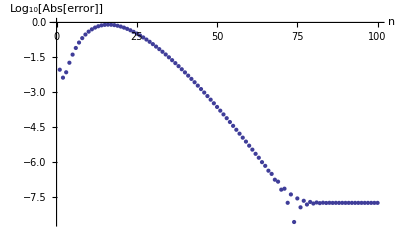

FittedModel[4.498-0.162569 x]

```mathematica
max = 100;
(*sk2convArraym = Array[sk2[α1,β2,γ2,τ,0,#,0]&,{max}]*)
sk2convArrayk = Array[sk2[α1,β2,γ2,τ,0,7,#]&,{max}];
lp1 = ListPlot[Table[{n,Log[10,Abs[sk2convArrayk[[n]]-s0val]]},{n,max}],AxesLabel->{n,"Log_10[Abs[error]]"}]
(*Export["",lp1]*)
LinearModelFit[Table[{n,Log[10,Abs[sk2convArrayk[[n]]-s0val]]},{n,50,55}],x,x]
```

```mathematica
Rationalize[.16]
```

4/25

{-0.423002,-0.416401,-0.416985,-0.416951,-0.416949,-0.41695,-0.41695,-0.41695}

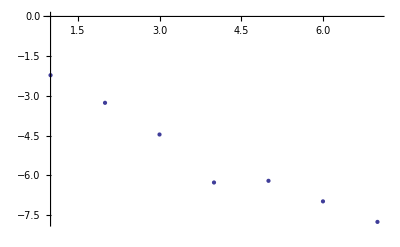

FittedModel[-1.17582-1.04228 x]

{-8.88178×10^-16,-8.88178×10^-16}

```mathematica
max = 8;
sk2convArraym = Array[sk2[α1,β2,γ2,τ,0,#,200]&,{max}]
ListPlot[Table[{n,Log[10,Abs[sk2convArraym[[n]]-s0val]]},{n,max-1}]]
lmf2 = LinearModelFit[Table[{n,Log[10,Abs[sk2convArraym[[n]]-s0val]]},{n,1,2}],x,x]
lmf2["FitResiduals"]
```

```mathematica
minm =1;maxm = 5;
mink=50;maxk = 100;
stuff = Array[sk2[α1,β2,γ2,τ,0,#1,#2]&,{10,100}];
```

$Aborted

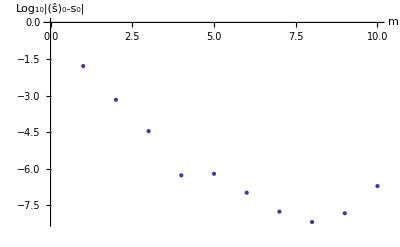

FittedModel[-2.60558-0.93693 x]

```mathematica
skconvplot= ListPlot[Table[Log[10,Abs[sk2[α1,β2,γ2,τ,0,n,n^4]-s0val]],{n,1,10}],AxesLabel->{m,"Log_10|(ŝ)_0-s_0|"},PlotRange->Automatic]
skconvArraymm5 = Array[Log[10,Abs[sk2[α1,β2,γ2,τ,0,#,#^4]-s0val]]&,{8}];
LinearModelFit[Table[skconvArraymm5[[n]],{n,2,6}],x,x]
Export["mkErrorConv.pdf",skconvplot];
```

```mathematica
(* verify it all works! *)
kkmax = 2;
(*Array[sk[α,β,γ,τ1,τ2,#-kkmax-1,4,1024]&,{2 kkmax}]//AbsoluteTiming*)
Array[sk2[α1,β2,γ2,τ,#-kkmax-1,5,400]&,{2 kkmax}]//AbsoluteTiming
FindRoot[s-α-β E^{-s τ1}-γ E^(-s τ2),{s,-.5}]
```

{7.436489,{-0.807007-2.76624 ⅈ,-0.619197-1.25181 ⅈ,-0.416949,-0.619197+1.25181 ⅈ}}

{s→-0.41695}

```mathematica
kmax = 5;
skArray = Array[sk2[α1,β2,γ2,τ,#-kmax-1,10,1000]&,{2kmax}]
```

{-1.05442-7.45943 ⅈ,-0.995385-5.89064 ⅈ,-0.918151-4.32437 ⅈ,-0.807007-2.76624 ⅈ,-0.619197-1.25182 ⅈ,-0.41695,-0.619197+1.25182 ⅈ,-0.807007+2.76624 ⅈ,-0.918151+4.32437 ⅈ,-0.995385+5.89064 ⅈ}

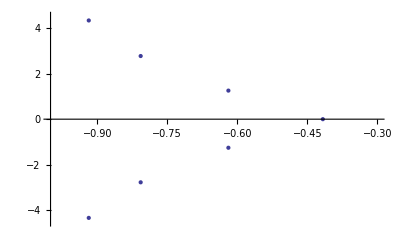

computedEvalsForTwoDelays.pdf

```mathematica
skvalplot = ListPlot[Table[{Re[skArray[[n]]],Im[skArray[[n]]]},{n,3,2 kmax-1}],PlotRange->{{-1,-.3},{-4.5,4.5}}]
Export["computedEvalsForTwoDelays.pdf",skvalplot]
```

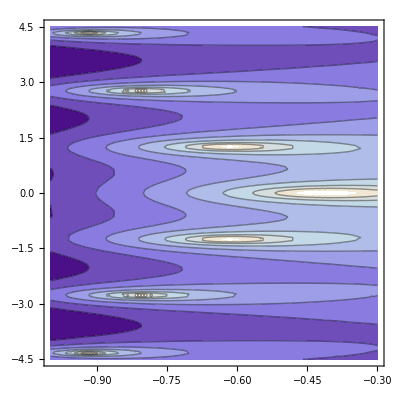

actualEvalsForTwoDelays.pdf

```mathematica
skcontplot =ContourPlot[Log[10,Abs[1/((s1+I s2)-α1-β1 E^(-s1-s2 I)-γ1 E^(-s1 τ -s2 τ I))]],{s1,-1,-.3},{s2,-4.5,4.5}]
Export["actualEvalsForTwoDelays.pdf",skcontplot]
```

```mathematica
Clear[rval,a1val,a2val,tauval]
rval=1;a1val=2;a2val=a1val;
FindMinimum[(Re[skComp[0,-rval a1val/(a1val+a1val),-rval a1val/(a1val+a1val),10,tauval,0,4,150]])^2,{{tauval,.01}}]
```

CompiledFunction::cfsa: Argument tauval at position 5 should be a "machine-size real number".

{3.42495×10^-29,{tauval→0.379414}}

{0.283298,3.48441×10^-17}

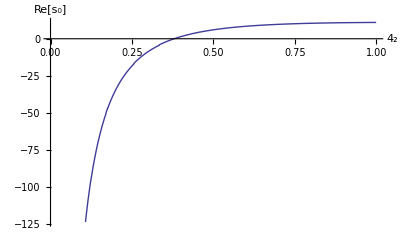

EvalVsTauPlot.pdf

```mathematica
Clear[tauval]
rval= 1;a1val =2;a2val =a1val;xstar=1/(a1val+a2val);T1 = 10;T2 = 0.420836;
alpha = 0;beta = -rval xstar a1val;gamma = -rval xstar a2val;
tauratio = T2/T1;alpha1 = alpha T1;beta1 = beta T1;gamma1 = gamma T1;
beta2 = beta1 Exp[-alpha1];gamma2 = gamma1 Exp[-alpha1 tauratio];
{N[1/Abs[Log[gamma2]]],Abs[N[beta2 gamma2^((-1)/tauratio)/Log[gamma2]]]}
evalVstauPlot = Plot[Re[skComp[0,-rval a1val xstar,-rval a2val xstar ,10,t2val,0,4,100]],{t2val,.01,1},AxesLabel->{Subscript[τ, 2],"Re[s_0]"},PlotRange->Automatic]
Export["EvalVsTauPlot.pdf",evalVstauPlot]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 260.55.

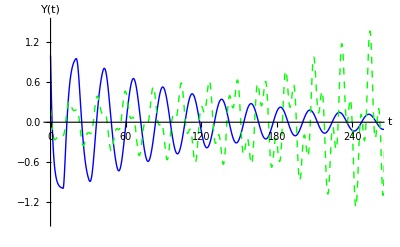

StableUnstableSolnPlot.pdf

```mathematica
r= 1;a1 =2;a2 =a1;T1 = 10;T2 = .2;
{xstar=1/(a1+a2),A1=r a1 xstar;A2=r a2 xstar,T1,1/(2 A1)};tmax = 300;
(*solx = NDSolve[{x'[t]==r  x[t](1-a1 x[t-T1]-a2 x[t-T2]),x[t/;t≤0]==.1+1/(a1+a2)},x,{t,0,200}];
solX = NDSolve[{X'[t]==-(1+X[t])(A1 X[t-T1]+A2 X[t-T2]),X[t/;t≤0]==(xstar+.1)/xstar-1},X,{t,0,200}];
soly = NDSolve[{y'[t]==-r (y[t]+xstar)(a1 y[t-T1] + a2 y[t-T2]),y[t/;t≤0]==.1},y,{t,0,200}];*)
solnY1 = NDSolve[{Y'[t]==-r xstar a1 Y[t-T1]-r xstar a2 Y[t-T2],Y[t/;t≤0]==1},Y,{t,0,tmax}];
r= 1;a1 =2;a2 =a1;T1 = 10;T2 = 1.3;{xstar=1/(a1+a2),A1=r a1 xstar;A2=r a2 xstar,T1,1/(2 A1)};
solnY2 = NDSolve[{Y'[t]==-r xstar a1 Y[t-T1]-r xstar a2 Y[t-T2],Y[t/;t≤0]==.2},Y,{t,0,tmax}];
solnplot = Plot[{Evaluate[{Y[t]}/.First[solnY1]],Evaluate[{Y[t]}/.First[solnY2]]},{t,0,tmax},PlotRange->{{0,260},{ -1.5,1.5}},PlotStyle->{{Blue, Thick},{Green,Dashed,Thick},{Red,Thick,Dotted}},AxesLabel->{t,"Y(t)"}]
Export["StableUnstableSolnPlot.pdf",solnplot]
```

```mathematica
Clear[α,β,γ,α1,β1,γ1,β2,γ2,τ,τ1,τ2]
β2=.001;γ2=6;τ=4;τ1 =1;α1=-1;τ2 = τ τ1;
α=α1/τ1;β =β2 E^α1 /τ1;γ=N[E^(α1 τ2/τ1) γ2/τ1];β1=β τ1;γ1=γ τ1;
stabcontourabt2=ContourPlot3D[Re[sk[alpha,beta,γ,τ1,tau2,0,4,100]]==0,{alpha,-5,5},{beta,-5,5},{tau2,.01,2.2},Mesh->None,ContourStyle->Opacity[0.4],AxesLabel->{"α","β","τ_2"},PerformanceGoal->"Quality"]
Export["StabilityContourAlphaBetaTau22.pdf",stabcontourabt2]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
(*Here is the code that I put in the paper*)
Clear[Logn,f2p,z,j,w,tau1,tau2,alpha,beta,gamma,k,l,m,n]
Clear[p,q,mmax,kmax,DBellYq,sigma,c,mu,sj,sjMem]
Logn[z_,j_]:=Log[Abs[z]]+Arg[z]+2*Pi*I*j;
f2p[w_,tau1_,tau2_,j_,c_]:=(-1)^j*(E^(-w)+c*(1/(E^(w*(tau1/tau2))*(tau2/tau1)^j)));
DBellYq[l_,p_,q_,tau1_,tau2_,c_]:=If[l<0||p<0||(p==0&&l>0)||l<p,0,If[q==0,BellY[l,p,Array[f2p[0,tau1,tau2,#1,c]&,{l-p+1}]],Sum[Binomial[l,r]*Sum[Binomial[q-1,s]*DBellYq[l-r,p-1,q-1-s,tau1,tau2,c]*f2p[0,tau1,tau2,1+r+s,c],{s,0,q-1}],{r,1,l-p+1}]]];
sigma[alpha_,gamma_,tau1_,tau2_,j_]:=1/Logn[gamma*tau1*Exp[(-alpha)*tau2],j];
c[alpha_,beta_,gamma_,tau1_,tau2_,j_]:=(beta*(Exp[alpha*(tau2-tau1)]/gamma))*(gamma*tau2*(Exp[(-alpha)*tau2]/Logn[gamma*tau1*Exp[(-alpha)*tau2],j]))^(1-tau1/tau2);
mu[alpha_,beta_,gamma_,tau1_,tau2_,j_]:=(Log[tau2/tau1]+Log[1/Logn[gamma*tau1*Exp[(-alpha)*tau2],j]])/Logn[gamma*tau1*Exp[(-alpha)*tau2],j]-c[alpha,beta,gamma,tau1,tau2,j];
sjcp[alpha_,beta_,gamma_,tau1_,tau2_,j_,mmax_,kmax_]:=(Logn[gamma*tau1*Exp[(-alpha)*tau2],j]+Log[tau2/tau1]-Log[Logn[gamma*tau1*Exp[(-alpha)*tau2],j]]+Sum[Sum[(Sum[Sum[Sum[(-1)^p Pochhammer[m,k]*((k+m)*Gamma[m]*Gamma[m-p]*Gamma[k+m+p])/(l!*q!*Gamma[2+k+l]*Gamma[-l+m]*Gamma[-1-l+2*m-q])*BellY[2*m-2-l-q,m-1-p,Array[f2p[0,tau1,tau2,#1,c[alpha,beta,gamma,tau1,tau2,j]]&,{Max[0,m-l-q+p]}]]*DBellYq[l,p,q,tau1,tau2,c[alpha,beta,gamma,tau1,tau2,j]],{q,0,2*m-2-l}],{p,0,l}],{l,0,m-1}]/(f2p[0,tau1,tau2,1,c[alpha,beta,gamma,tau1,tau2,j]]^(2*m+k-1)))*mu[alpha,beta,gamma,tau1,tau2,j]^m*(sigma[alpha,gamma,tau1,tau2,j]^k/m!/k!),{m,1,mmax}],{k,0,kmax}])/(tau2/tau1)+alpha*tau1;
```

```mathematica
(*Make sure this actually works*) 
N[sk[1,-1,1,1,2,0,5,100]]
N[sjcp[1,-1,1,1,2,0,5,100]]
N[sjsimp[1,-1,1,1,2,0,5,100]]
```

-0.243338-1.2026 ⅈ

-0.243338-1.2026 ⅈ

-0.243338-1.2026 ⅈ

```mathematica
FullSimplify[(m-1)! (k+m)! (m-p-1)! Pochhammer[k+m,p]/(l! (m-1-l)!q! (-l+2 m-2-q)! (k+l+1)!m!k!),Assumptions->{k∈Integers,l∈Integers,m∈Integers,p∈Integers,m≥1,k≥0,l≥0,p≥0,l≤ m-1,q≤ 2 m-2-l,p≤ l}]
```

((k+m) Gamma[m] Gamma[m-p] Gamma[k+m+p])/(k! l! m! q! Gamma[2+k+l] Gamma[-l+m] Gamma[-1-l+2 m-q])